```mathematica
NDEigensystem[{-1/2 Laplacian[u[x],{x}]+1/2 x^2 u[x],DirichletCondition[u[x]==0,True]},u[x],{x,-10,10},Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.5}}}}]
```

NDEigensystem[{1/2 x^2 u[x]-u''[x]/2,DirichletCondition[u[x]==0,True]},u[x],{x,-10,10},Method→{SpatialDiscretization→{FiniteElement,{MeshOptions→{MaxCellMeasure→0.5}}}}]

```mathematica
{vals,funs}=NDEigensystem[{-1/2 Laplacian[u[x],{x}]+1/2 x^2 u[x]+NeumannValue[-.5u[x],x==0]},u,{x,0,4π},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->.05}}}}]
```

{{-0.342419,2.22077,4.29123,6.32578,8.34733,10.3624,12.3738,14.3827,16.39,18.3961},{InterpolatingFunction[{{0., 12.5664}}, <>],InterpolatingFunction[{{0., 12.5664}}, <>],InterpolatingFunction[{{0., 12.5664}}, <>],InterpolatingFunction[{{0., 12.5664}}, <>],InterpolatingFunction[{{0., 12.5664}}, <>],InterpolatingFunction[{{0., 12.5664}}, <>],InterpolatingFunction[{{0., 12.5664}}, <>],InterpolatingFunction[{{0., 12.5664}}, <>],InterpolatingFunction[{{0., 12.5664}}, <>],InterpolatingFunction[{{0., 12.5664}}, <>]}}

```mathematica
NumberForm[vals,10]
```

{0.500000008,2.500000201,4.500001038,6.500003031,8.500006694,10.50001254,12.50002107,14.50003281,16.50004826,18.50006793}

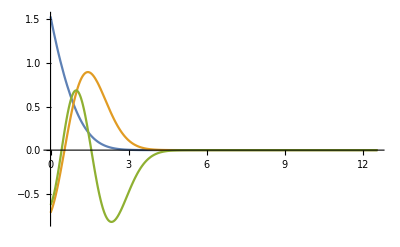

```mathematica
Plot[{funs[[1]][x],funs[[2]][x],funs[[3]][x]},{x,0,4π},PlotRange->All]
```

```mathematica
TestNDEigErrors[eps_,xmax_]:=
Module[{vals,funs},{vals,funs}=NDEigensystem[{-1/2 Laplacian[u[x],{x}]+1/2 x^2 u[x]},u,{x,-xmax,xmax},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->eps}}}}];
err=Abs[vals - {0.5,1.5,2.5,3.5}]
]
```

```mathematica
errs=TestNDEigErrors[.01,8π]
```

{1.19698×10^-11,9.03626×10^-11,3.25029×10^-10,8.19309×10^-10}

```mathematica
MeshSize=Table[eps,{eps,0.01,0.5,0.01}];neps=Length[MeshSize];
```

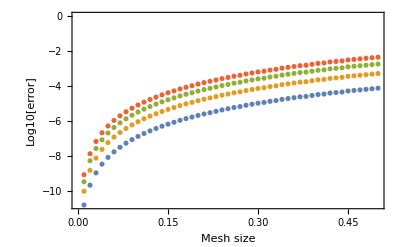

```mathematica
ListPlot[Table[{MeshSize[[n]],Log10[TestNDEigErrors[MeshSize[[n]],4π][[i]]]},{i,1,nmax},{n,1,neps}],Frame->True,FrameLabel->{"Mesh size","Log10[error]"}]
```

## Zero-range boundary conditions

Let’s see if we can get the zero-range boundary condition using the “Robin boundary condition” imposed with the NeumannValue function.

```mathematica
{vals,funs}=NDEigensystem[{-Laplacian[u[x],{x}]+Piecewise[{{10000,x>10},{0,x<10}}]u[x]+NeumannValue[-1u[x],x==0]},u,{x,0,20},5,Method->{"FEAST"}]
```

{{0.120816,0.474283,-0.998742,1.0462,1.83043},{InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>]}}

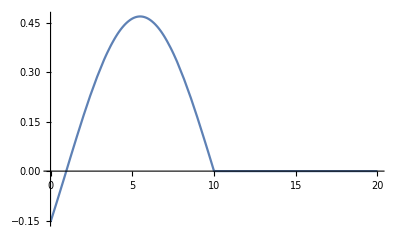

```mathematica
Plot[funs[[1]][x],{x,0,20}]
```

```mathematica
DEigensystem[{-Laplacian[u[x],{x}],DirichletCondition[u[x]==0,True]},u[x],{x,0,10},4]
```

{{π^2/100,π^2/25,(9 π^2)/100,(4 π^2)/25},{Sin[(π x)/10],Sin[(π x)/5],Sin[(3 π x)/10],Sin[(2 π x)/5]}}

```mathematica
{vals,funs}=DEigensystem[-Laplacian[u[x],{x}]+NeumannValue[-10u[x],x==0],u,{x,0,∞},5]
```

Set::shape: Lists {vals,funs} and DEigensystem[NeumannValue[-10 u[x],x==0]-u''[x],u,{x,0,∞},5] are not the same shape.

DEigensystem[NeumannValue[-10 u[x],x==0]-u''[x],u,{x,0,∞},5]

{{0.0249226,0.0996901,0.224302,0.398757,0.623052},{InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>]}}

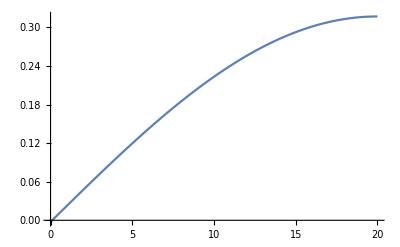

```mathematica
{vals,funs}=NDEigensystem[{-Laplacian[u[x],{x}]+NeumannValue[-10u[x],x==0],DirichletCondition[u[x]==0,x==20]},u,{x,0,20},5,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->.01}}}}]
```

```mathematica
D[funs[[1]][x],x]/funs[[1]][x]/.x->0
```

-10.0001

```mathematica
NDEigensystem[{-Laplacian[u[x],{x}],DirichletCondition[u[x]==0,True]},u[x],{x,0,10},Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.5}}}},5]
```

NDEigensystem[{-u''[x],DirichletCondition[u[x]==0,True]},u[x],{x,0,10},Method→{SpatialDiscretization→{FiniteElement,{MeshOptions→{MaxCellMeasure→0.5}}}},5]

```mathematica
un=NDEigensystem[{D[-u[x],x,x]==0-NeumannValue[u[x],x==1],DirichletCondition[u[x]==0,x==0]},u,{x,0,1}]
```

NDEigensystem[{-u''[x]==-NeumannValue[u[x],x==1],DirichletCondition[u[x]==0,x==0]},u,{x,0,1}]

```mathematica
CalcCotanDelta[v0_?NumberQ,r0_?NumberQ,ksqr_?NumberQ,rmax_?NumberQ]:=
Module[{vlocal,CotanDelta,sol,k,u1,u2,r1,r2},
r1=0.95 rmax;
r2=0.99rmax;
vlocal=v0;
k=√ksqr;
sol=NDSolve[{-u''[r]+vlocal Exp[-r^2/r0^2]u[r]==ksqr u[r],u[0]==0,u'[0]==1},u,{r,0,rmax}];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]
```

```mathematica
CalcERE[v0_,r0_,rmax_,ksqrMin_,ksqrMax_]:=
Module[{vlocal,EREData,ascat,reff,A,B,fitpars,dE},
dE=(ksqrMax-ksqrMin)/10;
vlocal=v0;
EREData=Table[{ksqr,√ksqr CalcCotanDelta[vlocal,r0,ksqr,rmax]},{ksqr,ksqrMin,ksqrMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff}]
]
```

```mathematica
r0=1;a2r2=Table[(blah=CalcERE[v0,r0,5*r0,.000001,.001];{{v0,blah[[1]]},{v0,blah[[2]]}}),{v0,0,-100,-1}];
```

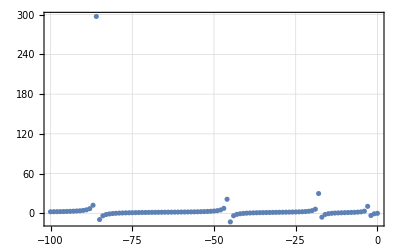

```mathematica
ListPlot[Transpose[a2r2][[1]],Frame->True,LabelStyle->Medium,GridLines->Automatic,PlotRange->All]
```

## complex absorbing potentials...?

```mathematica
W[x_,xc_]:=Piecewise[{{0,x<xc},{(x-xc)^2,x≥xc}}]
```

```mathematica
θ=0.25π;RotatedCont=Table[r Cos[θ]-I r Sin[θ],{r,0,2,.1}];
```

```mathematica
xmax=10;xc=5;η=.05;v0=7.5;{vals,funcs}=NDEigensystem[{-1/2 Laplacian[u[x],{x}]+(v0 x^2 Exp[-x]-I η W[x,xc]) u[x],DirichletCondition[u[x]==0,True]},u[x],{x,0,xmax},50,Method->{"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.02}}}}];
```

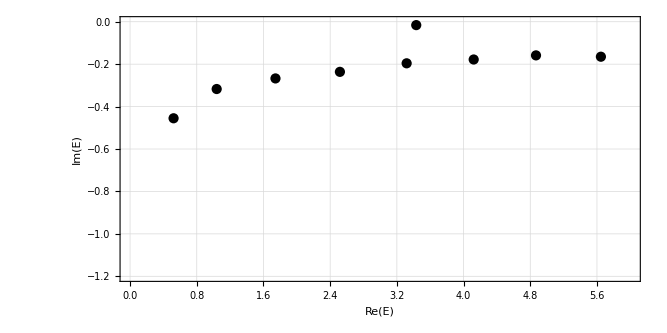

```mathematica
ComplexListPlot[{
vals
(*{4.834638875007031-1.1136182072294853 ⅈ,3.426388621176832-0.012776878261531332 ⅈ}*)
(*,RotatedCont*)},
PlotRange->{{0,6},{-1.2,0}},AspectRatio->1/2,Frame->True,LabelStyle->Large,GridLines->Automatic,FrameLabel->{"Re(E)","Im(E)"},PlotStyle->{{Black},{Red}}]
```

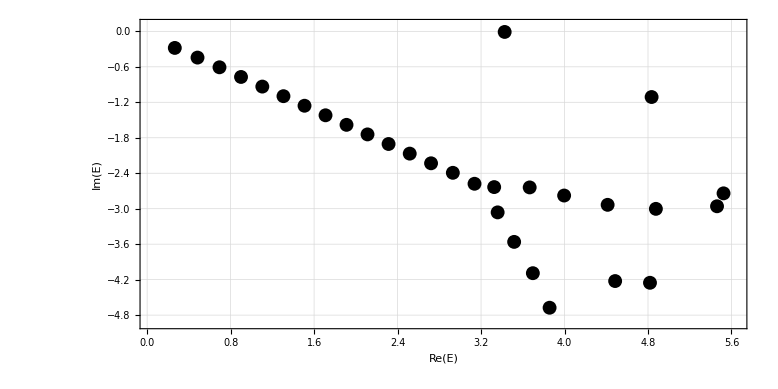

```mathematica
vals
```

{0.265103-0.283147 ⅈ,0.482718-0.446584 ⅈ,0.693236-0.610728 ⅈ,0.899678-0.774286 ⅈ,1.10376-0.937109 ⅈ,1.30644-1.09932 ⅈ,1.50826-1.26111 ⅈ,1.70959-1.42267 ⅈ,1.91071-1.58422 ⅈ,2.11194-1.74599 ⅈ,2.31367-1.90822 ⅈ,2.5165-2.07101 ⅈ,3.42639-0.0127769 ⅈ,2.72091-2.23463 ⅈ,2.92972-2.39568 ⅈ,3.13741-2.58097 ⅈ,3.32587-2.6371 ⅈ,3.66614-2.6426 ⅈ,3.35909-3.06487 ⅈ,3.99622-2.7799 ⅈ,4.83464-1.11362 ⅈ,3.51714-3.56401 ⅈ,4.41316-2.93715 ⅈ,3.69655-4.09335 ⅈ,4.87563-3.00525 ⅈ,3.85695-4.6777 ⅈ,4.48517-4.22655 ⅈ,5.524-2.74292 ⅈ,5.4616-2.96157 ⅈ,4.8191-4.25574 ⅈ}

```mathematica
{4.834638875007031-1.1136182072294853 ⅈ,3.426388621176832-0.012776878261531332 ⅈ}
```

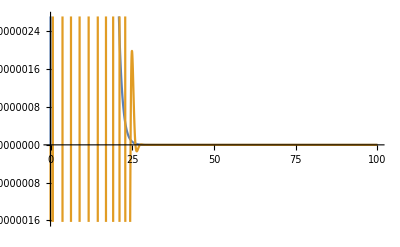

```mathematica
Plot[{7.5 x^2 Exp[-x],Re[funcs[[5]]]},{x,0,xmax}]
```

## 3D Oscillator states

Specify a Schrödinger operator with parameter h and potential V:

```mathematica
V[x_,y_,z_,kxy_]:=1/2(x^2+y^2+z^2)+kxy (x^2 y^2+.5 x^2 z^2 +.25 y^2 z^2)
```

Find the 10 smallest eigenvalues and eigenfunctions on a refined mesh:

```mathematica
kvals=Table[k,{k,0,2,0.05}];
Asymevals=Table[NDEigensystem[-1/2 Laplacian[u[x,y,z],{x,y,z}]+V[x,y,z,kxy]*u[x,y,z],u[x,y,z],{x,-5,5},{y,-5,5},{z,-5,5},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.1}}}}][[1]],{kxy,kvals}]
```

{{1.50016,2.50049,2.50049,2.50049,3.50083,3.50083,3.50144,3.50144,3.50146,4.50118},{1.52124,2.53933,2.55066,2.5566,3.55422,3.5637,3.58012,3.59765,3.61084,3.63068},{1.54093,2.57515,2.59606,2.60739,3.60244,3.62033,3.65133,3.68438,3.70504,3.74411},{1.5595,2.6086,2.63788,2.65419,3.64716,3.67273,3.71666,3.76369,3.78891,3.84613},{1.57713,2.64011,2.67689,2.69783,3.68907,3.72176,3.77741,3.83723,3.86512,3.93956},{1.59396,2.67,2.7136,2.73887,3.72866,3.76803,3.83446,3.90608,3.93537,4.0262},{1.61009,2.6985,2.74837,2.77772,3.76628,3.81195,3.8884,3.97102,4.00078,4.10729},{1.6256,2.72577,2.78149,2.81469,3.80219,3.85387,3.93969,4.03261,4.06219,4.18371},{1.64056,2.75198,2.81315,2.85003,3.83661,3.89402,3.9887,4.09132,4.12019,4.25616},{1.65502,2.77723,2.84354,2.88392,3.8697,3.93261,4.03568,4.14748,4.17526,4.32515},{1.66903,2.80162,2.8728,2.91653,3.90161,3.96982,4.08087,4.20139,4.22777,4.39109},{1.68264,2.82522,2.90103,2.94797,3.93245,4.00577,4.12445,4.25329,4.27802,4.45434},{1.69586,2.84812,2.92833,2.97837,3.96233,4.04058,4.16658,4.30336,4.32626,4.51518},{1.70873,2.87036,2.9548,3.0078,3.99131,4.07435,4.20738,4.35177,4.37269,4.57383},{1.72128,2.89199,2.98048,3.03636,4.01948,4.10717,4.24696,4.39868,4.41748,4.63049},{1.73353,2.91307,3.00546,3.06412,4.0469,4.1391,4.28543,4.44419,4.46078,4.68535},{1.7455,2.93363,3.02977,3.09112,4.07362,4.17021,4.32286,4.48842,4.50272,4.73854},{1.7572,2.9537,3.05348,3.11743,4.09969,4.20057,4.35933,4.53145,4.5434,4.79019},{1.76865,2.97333,3.0766,3.14309,4.12515,4.23021,4.39491,4.57339,4.58293,4.84043},{1.77987,2.99252,3.0992,3.16815,4.15005,4.25919,4.42966,4.61428,4.62139,4.88934},{1.79087,3.01131,3.12129,3.19263,4.17441,4.28754,4.46362,4.65422,4.65884,4.93702},{1.80166,3.02973,3.14291,3.21659,4.19828,4.3153,4.49684,4.69324,4.69537,4.98354},{1.81226,3.04779,3.16409,3.24004,4.22167,4.34251,4.52937,4.73102,4.73141,5.02898},{1.82266,3.0655,3.18484,3.26301,4.24461,4.36919,4.56125,4.76586,4.76878,5.0734},{1.83288,3.0829,3.2052,3.28553,4.26712,4.39537,4.5925,4.79992,4.80538,5.11687},{1.84294,3.09999,3.22518,3.30763,4.28923,4.42108,4.62317,4.83326,4.84126,5.15942},{1.85283,3.11679,3.2448,3.32932,4.31096,4.44634,4.65327,4.86592,4.87646,5.20112},{1.86256,3.13331,3.26408,3.35063,4.33232,4.47117,4.68284,4.89792,4.91101,5.242},{1.87215,3.14956,3.28303,3.37156,4.35334,4.49558,4.71191,4.92931,4.94493,5.28211},{1.88159,3.16556,3.30167,3.39215,4.37402,4.51961,4.74049,4.96011,4.97827,5.32148},{1.89089,3.18132,3.32001,3.41239,4.39438,4.54326,4.76861,4.99036,5.01104,5.36015},{1.90007,3.19684,3.33806,3.43232,4.41443,4.56656,4.79628,5.02008,5.04327,5.39816},{1.90911,3.21214,3.35585,3.45194,4.43419,4.5895,4.82353,5.04928,5.07499,5.43552},{1.91803,3.22722,3.37337,3.47126,4.45367,4.61212,4.85037,5.07801,5.10621,5.47227},{1.92684,3.24209,3.39063,3.4903,4.47288,4.63442,4.87682,5.10627,5.13695,5.50843},{1.93553,3.25676,3.40766,3.50906,4.49183,4.65641,4.90289,5.13408,5.16724,5.54403},{1.94411,3.27124,3.42445,3.52756,4.51052,4.67811,4.9286,5.16147,5.19709,5.57908},{1.95258,3.28554,3.44101,3.54581,4.52898,4.69952,4.95395,5.18846,5.22652,5.61362},{1.96095,3.29965,3.45736,3.56381,4.5472,4.72066,4.97898,5.21504,5.25553,5.64766},{1.96923,3.3136,3.4735,3.58158,4.56519,4.74153,5.00367,5.24125,5.28416,5.68122},{1.9774,3.32737,3.48944,3.59912,4.58297,4.76215,5.02805,5.2671,5.31241,5.71431}}

```mathematica
sortedevals=Table[Sort[Asymevals[[i]]],{i,1,Length[kvals]}];
```

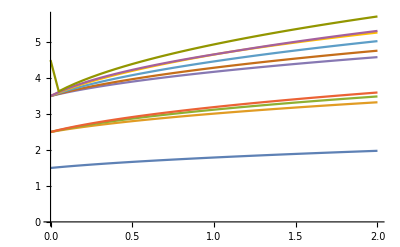

```mathematica
ListPlot[Table[Table[{kvals[[i]],sortedevals[[i,j]]},{i,1,Length[kvals]}],{j,1,10}],Joined->True]
```

```mathematica
V[x_,y_,z_]:=1/2(x^2+y^2+z^2)
ℒ=-1/2 Laplacian[u[x,y,z],{x,y,z}]+V[x,y,z]*u[x,y,z];
```

Find the 10 smallest eigenvalues and eigenfunctions on a refined mesh:

```mathematica
{vals,funs}=NDEigensystem[ℒ,u[x,y,z],{x,-4,4},{y,-4,4},{z,-4,4},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.1}}}}]
```

{{1.50015,2.50043,2.50043,2.50043,3.50072,3.50072,3.50109,3.50109,3.5011,4.50103},{InterpolatingFunction[{{-4., 4.}, {-4., 4.}, {-4., 4.}}, <>][x,y,z],InterpolatingFunction[{{-4., 4.}, {-4., 4.}, {-4., 4.}}, <>][x,y,z],InterpolatingFunction[{{-4., 4.}, {-4., 4.}, {-4., 4.}}, <>][x,y,z],InterpolatingFunction[{{-4., 4.}, {-4., 4.}, {-4., 4.}}, <>][x,y,z],InterpolatingFunction[{{-4., 4.}, {-4., 4.}, {-4., 4.}}, <>][x,y,z],InterpolatingFunction[{{-4., 4.}, {-4., 4.}, {-4., 4.}}, <>][x,y,z],InterpolatingFunction[{{-4., 4.}, {-4., 4.}, {-4., 4.}}, <>][x,y,z],InterpolatingFunction[{{-4., 4.}, {-4., 4.}, {-4., 4.}}, <>][x,y,z],InterpolatingFunction[{{-4., 4.}, {-4., 4.}, {-4., 4.}}, <>][x,y,z],InterpolatingFunction[{{-4., 4.}, {-4., 4.}, {-4., 4.}}, <>][x,y,z]}}